Curtis Sera
v 2.2
2019 - 11- 14

# Bending energy of a toroidal pore

Solving the bending energy of a torus (ie the maximum energy conformation of a fusion pore)
Per MB Jackson (2010), a toroidal pore is a maximum energy conformation

Assume 0 spontaneous curvature for membrane
For complete work & derivations, see OneNote\Welch Lab\Work\Toroid Gbend 3

This notebook will compare 2 approaches, both in cylindrical coordinates:
A) Solving based on finding an expression for the distance between the z axis and the torus inner surface then spinning that around the z axis
	** z = 0 here set to the torus bottom
B) Solving based on a  parametrizing the surface integral so that it’s in terms of theta (renamed alpha) and the angle beta as below
	** z = 0 here set to the torus transverse midplane
 


Mathematica reminders/notes:
- () are for grouping, [] are for functions
- Functions conventionally start with CAPS.  Ie write Cos[], not cos[]

Definitions:
	r ~ distance b/w torus central axis & torus surface at that height
	R ~ torus ring radius
	t ~ tube radius (how thick the donut is)
	b ~ angle from midplane where 0 is the outer intersection b/w torus surface & midplane
	Kb ~ bending modulus

Graphing the surface:
First, let’s construct and graph the surface we’re computing things for so that we have something to project our results onto
To let us vary pore radius later, we’ll make this a function of both z and R0.

```mathematica
t = 5;  (*Radius of the torus's tube = distance b/w membranes; nm*)
R20 = 20;  (*First value for R0 as defined above; nm*)
Kb = 15;  (*Helfrich bending constant; k(_B)T*)
```

20-5 √(1-1/25 (5-z)^2)

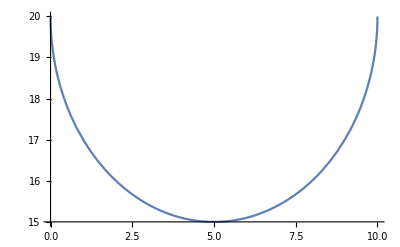

-Graphics3D-

```mathematica
r[z_,R_] := R-t Cos[ArcSin[(t-z)/t]];(*torus's local radius of curvature in plane of R*)

torus = r[z,R20]
Plot[torus,{z,0,2*t}]
RevolutionPlot3D[{torus,z},{z,0,2*t}] 
	(*Note how we put pwR as "x" and put z last to make it the axis of revolution*)
```

Method A: Bending energy by torus profile 
Great!
Now let’s compute the bending energy (which induces an equivalent tension)...
First, we’ll get the bending energy per unit area of the surface. So that we can adjust R later, we’ll make that an input var too

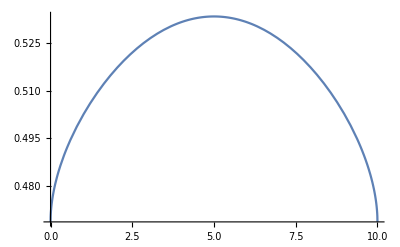

```mathematica
GbendAArea[z_,R_]:= Kb*0.5*(((1/t)+(1/r[z,R]))^2) (*Gbend per unit area. What we'll use to show stress on the toroid surface*)

Plot[GbendAArea[z,R20],{z,0,2*t}]
```

Note how per unit area peaks at z=t since most bent there, but the ring energy peaks at the ends (z=0,2t) since the area change is relatively large vs GendAArea’s change over z

Next, we' ll re-graph our surface using above tension function as the coloring guide
- Color with normalized values

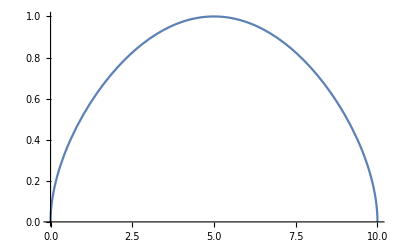

-Graphics3D-

```mathematica
GbendANormArea[z_,R_]:=(GbendAArea[z,R]-GbendAArea[0,R])/(GbendAArea[t,R]-GbendAArea[0,R]) (*Map Gbend to range [0,1] for graph coloring*)
Plot[GbendANormArea[z,R20],{z,0,2*t}]

tension3dPlot=RevolutionPlot3D[{torus,z},{z,0,2*t},
ColorFunction->Function[{x,y,z},
Hue[2(1-GbendANormArea[z,R20])/3]],ColorFunctionScaling->False]
```

Notes on Hue[]: 
- To make red correspond to the highest tension, we’ve inverted the scale via 1-GbendNormA[z]
- To fix the default scheme’s color weirdness (they have magenta/violet as the min which looks a lot like the max’s red), we’ve done 2/3 to basically cut out the magenta

Next, let’s use the torus’s rotational symmetry to get the Gbend for rings going up the z axis

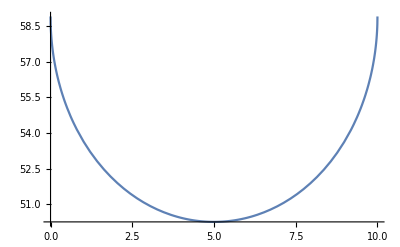

```mathematica
GbendARing[z_,R_]:= (2*Pi*r[z,R])*GbendAArea[z,R] (*GbendAArea integrated about the z axis at height z -> 2*Pi*r *)
	(*Will be used for subsequent calculation of pore energy *)
 
Plot[GbendARing[z,R20],{z,0,2*t}]
```

Finally, let' s use the above expression to get the toroidal pore' s total energy when R = 20 nm

```mathematica
Sum[GbendARing[z,R20],{z,0,2*t}]
```

582.119

Great! Now let' s look at how the total pore energy varies with pore radius (ie R - t)

582.119

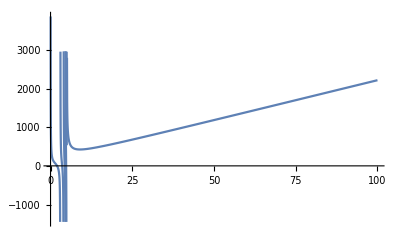

```mathematica
GbendAPore[R_]:=Sum[GbendARing[z,R],{z,0,2*t}]

GbendAPore[R20]

Plot[GbendAPore[R],{R,0,100}]
```

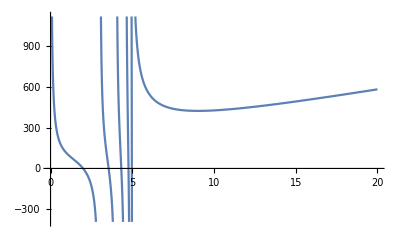

```mathematica
Plot[GbendAPore[z,R],{R,0,20}]
```

Well those plots sure seem wonky...

Method B: surface integral in parametric space

Note on integration in Mathematica:
- Integrate[f,x1,x2] can do definite or indefinite integration (see docs). Note that the integration order works left to right.
	- Eg Integrate[f,{x,0,Pi},{y,Pi/2,Pi}] --> does SS f() dx dy

```mathematica
Integrate[Kb*t*(1/t+1/(R-t*Cos[β]))^2,{α,0,2*Pi},{β,0,Pi/2}]
```

3 π (π+250/(R (-25+R^2))+(20 (-50+5 R+2 R^2) ArcTanh[(5+R)/(√(25-R^2))])/((25-R^2)^(3/2)))

The above should be equivalent to integrating over alpha then over beta which is functionally equivalent to the order used in method A.
Let’s check that it’s doing the intended order of integration by integrating over β after computing the integral over α by hand

```mathematica
Integrate[2*Pi*Kb*t*(1/t+1/(R-t*Cos[β]))^2,{β,0,Pi/2}]
```

ConditionalExpression[3 π (π+250/(R (-25+R^2))+(20 (-50+R (5+2 R)) ArcTanh[(5+R)/(√(25-R^2))])/((25-R^2)^(3/2))),(Re[ArcCos[R/5]]<0||Re[ArcSin[R/5]]<0||ArcSin[R/5]∉ℝ)&&(Re[R]>5||Re[R]<0||R∉ℝ)]

Uh... ok.  Not totally sure exactly what that means, but the essential expression is the same so it looks like Mathematica is integrating in the order I intended?

The surface integral should have interchangeable order of integration. Let’s check that

```mathematica
Integrate[Kb*t*(1/t+1/(R-t*Cos[β]))^2,{β,0,Pi/2},{α,0,2*Pi}]
```

ConditionalExpression[3 π (π+250/(R (-25+R^2))+(20 (-50+R (5+2 R)) ArcTanh[(5+R)/(√(25-R^2))])/((25-R^2)^(3/2))),(Re[ArcCos[R/5]]<0||Re[ArcSin[R/5]]<0||ArcSin[R/5]∉ℝ)&&(Re[R]>5||Re[R]<0||R∉ℝ)]

Still not totally sure what’s up with the conditional stuff, but at least all the main expressions are the same...

Since things are at least internally consistent, now let’s get the ball rolling by making the integral into a function we can call and plug things into.
We’ll make the function using the expression we’ve already computed since integration is computationally intensive

```mathematica
GbendB[R_]:=3Pi(Pi+250/(R((R^2)+-25))+(20(2(R^2)+5R-50)*ArcTanh[(5+R)/Sqrt[25-(R^2)]])/(25-(R^2))^1.5)
```

-75.5938+98.456 ⅈ

-Graphics-

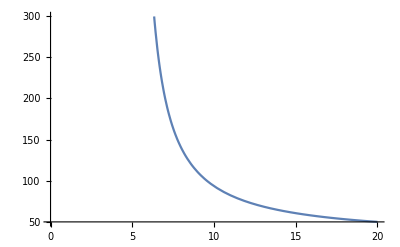

```mathematica
GbendB[2]
Plot[GbendB[R],{R,0,5}]
Plot[GbendB[R],{R,0,20}]
```

Well ... That' s certainly not the same graph that I got with method A ...